```mathematica
Reduce[Q z>(ρ Q)/4,ρ]
```

z∈ℝ&&((Q<0&&ρ>4 z)||(Q>0&&ρ<4 z))

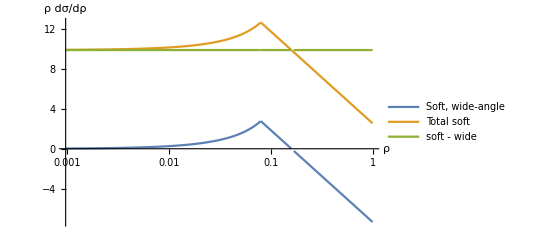

```mathematica
zval=0.04;
soft[ρ_,z_]:=(HeavisideTheta[ρ-2z](-3-4Log[ρ/2]+4Log[2])
+HeavisideTheta[2z-ρ](-3-4Log[z]-4Log[1-ρ/(4z)]));
softWide[ρ_,z_]:=4HeavisideTheta[ρ-2z]Log[(4z)/ρ]+4HeavisideTheta[2z-ρ]Log[z/(z-ρ/4)];
LogLinearPlot[{softWide[ρ,zval],soft[ρ,zval],soft[ρ,zval]-softWide[ρ,zval]},
{ρ,0,1},
AxesLabel->{"ρ","ρ dσ/dρ"},PlotLegends->{"Soft, wide-angle", "Total soft", "soft - wide"}]
```

```mathematica
Assuming[{0<ρ<1},FullSimplify[soft[ρ,z]-softWide[ρ,z]]]
```

-HeavisideTheta[-2 z+ρ] (3+4 Log[z])-HeavisideTheta[2 z-ρ] (3+4 Log[-z]+4 Log[z]-4 Log[-4 z+ρ]+4 Log[4-ρ/z])

#### Kinematics

```mathematica
gluon=q, quark=p1,antiq=p2
```

```mathematica
x1=(2p1 Q)/Q^2=(2p1 p2+2p1 q)/Q^2=(Q^2+2p1 q)/Q=1+qp/Q
```

```mathematica
x1=(2p1 Q)/Q^2=(2p1 p2+2p1 q)/Q^2=(Q^2-2p2 q)/Q^2=1-qm/Q
```

#### Phase space

```mathematica
int=2/Q^2 Integrate[HeavisideTheta[Q-(qp+qm)] 1/(2qp qm)Q DiracDelta[qm-(ρ Q)/4]HeavisideTheta[qp+qm-Qz]HeavisideTheta[qp-qm],{qm,0,Q},{qp,0,Q}]
```

```mathematica
intCollinear=2/Q^2 Integrate[HeavisideTheta[Q-qp] 1/(2qp qm)Q DiracDelta[qm-(ρ Q)/4]HeavisideTheta[qp-Qz]HeavisideTheta[qp],{qm,0,Q},{qp,0,Q}]
```